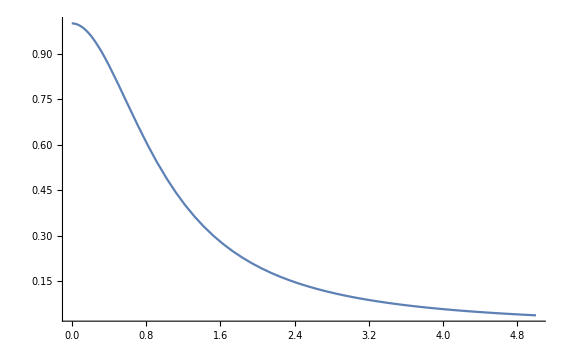

```mathematica
Plot[1/(1+x^2),{x,0,5},PlotRange->Full]
```

Idée principale

Approximer cos α ≈ e^(-x^2/2)

```mathematica
Series[Cos[x],{x,0,10}]
```

1-x^2/2+x^4/24-x^6/720+x^8/40320-x^10/3628800+O[x]^11

```mathematica
Series[Exp[-x^2/2],{x,0,10}]
```

1-x^2/2+x^4/8-x^6/48+x^8/384-x^10/3840+O[x]^11

```mathematica
Manipulate[Plot[{Cos[x]^s,Exp[-s x^2/2]},{x,0,π/2},PlotRange->{0,1}],{{s,4},0,64}]
```

Convolution de 2 gaussiennes : σ_0^2+σ_1^2=σ_2^2

Residues

From https://en.wikipedia.org/wiki/Residue_(complex_analysis)

```mathematica
Integrate[ⅈⅇ^(ⅈ(k+1)θ),{θ,0,2π}]
```

-(ⅈ (-1+ⅈⅇ^(2 ⅈ (1+k) π)))/((1+k) Log[ⅈⅇ])

```mathematica
Series[ⅈⅇ^(ⅈ(k+1)θ),{θ,0,10}]
```

1+ⅈ (1+k) Log[ⅈⅇ] θ-1/2 ((1+k)^2 Log[ⅈⅇ]^2) θ^2-1/6 ⅈ (1+k)^3 Log[ⅈⅇ]^3 θ^3+1/24 (1+k)^4 Log[ⅈⅇ]^4 θ^4+1/120 ⅈ (1+k)^5 Log[ⅈⅇ]^5 θ^5-1/720 ((1+k)^6 Log[ⅈⅇ]^6) θ^6-(ⅈ (1+k)^7 Log[ⅈⅇ]^7 θ^7)/5040+((1+k)^8 Log[ⅈⅇ]^8 θ^8)/40320+(ⅈ (1+k)^9 Log[ⅈⅇ]^9 θ^9)/362880-(((1+k)^10 Log[ⅈⅇ]^10) θ^10)/3628800+O[θ]^11

```mathematica
2π * Integrate[Cos[x]^n Sin[x],{x,0,π/2},Assumptions->n>0]
```

(2 π)/(1+n)

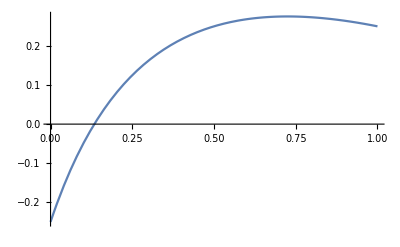

```mathematica
Plot[(3x)/(1+2x)-(x/2+1/4),{x,0,1}]
```